### Init v1

What is Wolfram’s take on biology?

There’s a lot of stuff out t

For anyone interested in this just wanted to give my takeaways from reading Wolfram’s stuff and working intensely with him on it.

Also if anyone has questions or thoughts just reach out or respond here.

In new kind of science, SW establishes a boundary, between simple systems and complex systems, which he determines based on just looking at the system visually. Here’s an example of a simple system:

```mathematica
ArrayPlot[CellularAutomaton[250,CenterArray[{1},33],15],Mesh->True,MeshStyle->GrayLevel[.15]]
```

-Graphics-

And here is his quintessential example of a complex system:

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},50],Mesh->False,MeshStyle->GrayLevel[.15]]
```

-Graphics-

And the claim is that the threshold from simple to complex is surprisingly low. So to generate the above it just takes 8 rules. But what you get is something with virtually unbounded complexity. And therefore, you’d imagine in the real world that this type of complex behavior is everywhere.

Relating this to biology, it is sometimes believed that all the intricate details of an organism are a result of selection. But because of how cheap complexity actually is, you’d imagine that many of these details are not essential to the functioning of the organism and are instead just side effects of computational irreducible behavior.

Pigmentation patterns of mollusc shells for example, are not exposed during the organisms lifetime and therefore have no effect on selection. But as you can see they are very complex and look remarkably similar to the behavior above.

-Graphics-

But even in cases where selection is acting on the behavior, you can still observe this phenomenon. For example, there was likely some selection pressure for a Jaguar to be somewhere in between black and yellow. But the exact location of the black and yellow spots isn’t a result of meticulous selection, rather it’s just a side effect of the computational irreducibility of the process that produces the pigmentation pattern.

#### v1

Generalizing the point, in biology, we have these irreducible systems trying to fit into the goals defined by selection, and so we get all this extra complexity that is not essential to the functioning of the organisms.

He even comments that natural selection, instead of selecting for very specific details, has the effect of simplifying the organisms

which in Wolfram’s view, is the reason why biology is so complicated as a field of study, with most experts specializing in some small segment of the field.

After NKS, SW was working on other projects like Wolfram Alpha and The Physics Project, but fast-forwarding 20 years he revisited biology, in particular, biological evolution.

In this recent work he “evolves” cellular automata to achieve the goal of “living” longer and longer:

This is done by changing the rules of the cellular automata randomly, one bit at a time, and keeping the changes that make the automaton “live” longer.

He uses this minimal example to make the claim that what evolution is doing, is finding pieces of irreducible computation, and putting them together to achieve some goal defined by the environment.

He therefore

Fast forwarding

an evolutionary observer that is taking a slice of all possible organisms, but evolution

The 

 which he calls the principle of computational equivalence. 

He then goes on to say that this demarcation between simple and complex is really the only two buckets that exist.

#### v2

So Wolfram seems to have nailed this interpretation

### outtakes

So the takeaway, is that these computationally irreducible systems are quite easy to generate and therefore are expected to be very frequent in nature.

SW takes this idea and applies it to biology.

He then argues that the complexity observed in these simple systems is as complex as any system. So even if you add more complicated rules, or more colors, or more dimensions or whatever, you still get something that is just really complicated. Taking this further, in trying to make predictions about the behavior, you find that there is no simpler model that can predict the pattern other than just running the rules. This he calls computational irreducibility.

### V3

So in NKS SW basically says that all the complexity we see in biology is not a result of a meticulous natural selection process, rather it is just a consequence of the fact that it is easy to generate complexity. Pigment patterns are an example of this, and one that SW explores thoroughly in NKS.

Growth is another example, where SW argues that the complexity and variation of form observed in biology is not a result of natural selection, but is instead a story of complexity being easy to find.

He uses growth leaves and leaf patterns. He shows models of shell and horn growth.

But can this complexity be reached by natural selection? To answer this, SW attempts to satisfy local constraints via a random iterative search, slowly changing the system bit by bit to try to satisfy more and more of the constraints. If one tries this without randoms, he shows that you get stuck before you can come close to solving the full problem. If one allows  some randomness, i.e. allowing changes that are neutral to the goal, then you are able to solve the problem. But even then, it sometimes takes a huge number of steps, suggesting that organisms would often not be able ever reach these complex patterns via a random iterative search process like natural selection.

At a high-level, SW suggests that when your landscape is computationally irreducible and messy, adaptive search doesn’t work very well, mentioning that he spent as much effort trying to get this constraint satisfaction thing to work as any other part of the book.

Since then, progress has been made on this problem both by SW scientifically and in the technological realm. So SW was mostly doing random changes in the iterative

at constraint satisfaction  that shows how

### V4

SW found that trying to use iterative search to satisfy anything but the simplest local constraints often runs into the problem of getting stuck at local maxima. You can get around this by adding randomness to the search, but this has the problem that it can take extremely long, and therefore you wouldn’t expect organisms to ever converge towards a complex solution that way.

All this to say that the detailed complexity cannot be explained by natural selection and instead is far more likely in most cases to rather just be a result of the fact that complexity is easy to find.

You may be wondering, how has this line of thinking aged with the advent of machine learning?

Successful machine learning works very similar to the approaches that SW tried, and in fact, he often mentions that he initially tried doing research with neural networks but found them to be too difficult to work with.

But we now know, on certain tasks, large neural networks perform much better than other adaptive approaches. Now this comes with a big caveat, and a lot of SW’s later work around biology has been around this question.

The point is that even large neural networks do not work well if the landscape you are trying to climb is too messy.

### V5

SW intensely pursued the problem of local constraints in NKS, but one breakthrough that was made was

### Computational biology: where we’ve been and where we’re going

Ever since I could remember I’ve always been interested in biological life forms, and in particular human life. I still remember in like 4th grade writing this essay about the wonders of the human body. How did our body work? How did our brain work? Why do we act the way we do?

And I think since then, and in particular in the last few months, I’ve made significant progress on answering some of my most burning questions in biology.

So after finishing another post with SW, and being asked to summarize the Wolfram view of biology,I figured I’d do this as my version of a vacation. And it didn’t disappoint, because of my rekindled excitement around biology, the writing and research of this piece was relatively easy, and quite enjoyable. So I hope you enjoy reading it as much as I did writing it.

In trying to tell the story of biology, I will skip the stuff that everyone already knows, like Darwin’s selection, DNA, the cell etc. and instead focus on the less mainstream but, in my view, equally important contributions. We will then use this alternative history as a jumping off point for the future of biology.

In doing this, what I’ve found, and what I think the reader will find, is that, like most things in life, the field of biology is full of surprises, and these surprises have tremendous implications for our current lives, and for the lives of the generations to come.

So okay that’s an ambitious goal, where do we start. Well everyone has heard Darwin’s idea of variation and selection, but can we be more precise about this. Well that’s really what the field of population genetics is. And it’s mainly in the language of math, but with the modern computational tools we can do much better. The core idea of population genetics, and really natural selection, is to imagine a 3-dimensional fitness landscape:

In the early 20th Century, the population geneticist Sewall Wright established the concept of the “fitness landscape”. The idea was to imagine a topology:

### V1 hills

```mathematica
SeedRandom[RandomGeneratorState[…]];hillCenters=RandomReal[{-10,10},{5,2}];
hillFunction[center_,x_,y_]:=Exp[-(Norm[{x,y}-center]^2)/12]; 
terrain[x_,y_]:=Total[hillFunction[#,x,y]&/@hillCenters];
clusterCenter={0,-4}; 
clusterPointsXY=RandomPoint[Disk[clusterCenter, 2], 20];
clusterPoints=Table[{p[[1]],p[[2]],3terrain[p[[1]],p[[2]]]+0.05},{p,clusterPointsXY}];
styled = Style[Point[#], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]]]&/@ clusterPoints;
```

```mathematica
Show[Plot3D[terrain[x,y],{x,-15,15},{y,-15,15},PlotRange->All,Mesh->None,ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False], Graphics3D[{PointSize[0.015],styled}]]
```

-Graphics3D-

```mathematica
Show[Plot3D[terrain[x,y]^1.5,{x,-15,15},{y,-15,15},PlotRange->{{-10, 0}, {-10, 0}, All},Mesh->None,ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False], Graphics3D[{PointSize[0.015],styled}]]
```

-Graphics3D-

```mathematica
survivors[pts_]:= TakeLargestBy[Last, 10]
```

```mathematica
ptslist = NestList[
With[{survivors = TakeLargestBy[#, Last, 10]}, 
Join[survivors, 
Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]](*+0.075*)}, {p, 
survivors[[All, ;;2]]+ RandomVariate[NormalDistribution[0, .5], {10, 2}]}]]]&, clusterPoints, 19];
```

```mathematica
slist = Map[Style[Point[#], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]]]&, ptslist, {2}];
gs = Show[Plot3D[terrain[x,y],{x,-15,15},{y,-15,15},PlotRange->All,Mesh->None,ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False], Graphics3D[{PointSize[0.015],#}]]&/@ slist;
```

```mathematica
GraphicsGrid[Partition[gs[[1;;All;;2]], 4]]
```

-Graphics-

```mathematica
ListAnimate[gs]
```

```mathematica
FindClusters[clusterPointsXY]
```

{{{-0.934701,3.5635},{-1.64028,2.94613},{-1.02376,3.14106}},{{0.189778,1.66023}},{{1.7064,1.8702},{0.944431,0.905301},{0.73781,0.868672},{1.39201,0.828201},{1.20285,1.53229}},{{-1.44908,0.642594},{-0.487797,0.619419},{-1.52977,1.17443},{-0.84297,0.380552},{-1.41684,0.890405},{-0.0303598,0.176853},{-1.30757,0.747248}},{{0.548903,2.80596},{0.086142,3.44556},{1.10021,3.04289}},{{-0.990245,1.84736}}}

```mathematica
findpops[pts_]:=
```

```mathematica
TakeLargestBy[Last, 10]
```

```mathematica
reproduce[center_]:=
```

```mathematica
evolve[pts_]:= Select[]
```

```mathematica
clusterPointsXY=3*RandomPoint[Rectangle[], 20, {{-10, 10}, {-10, 10}}];
```

```mathematica
clusterPointsXY=3RandomPoint[Rectangle[], 20, {}];
```

```mathematica
clusterPointsXY
```

{{0.741588,0.197333},{0.347052,0.244918},{0.956739,0.535804},{0.428649,0.903184},{0.979955,0.26688},{0.0908971,0.50843},{0.910295,0.361839},{0.465121,0.265487},{0.0832173,0.47326},{0.910742,0.396386},{0.00797159,0.310746},{0.401135,0.620481},{0.684546,0.473702},{0.799652,0.296534},{0.821597,0.965583},{0.0821226,0.932566},{0.986205,0.478148},{0.304578,0.0418198},{0.850463,0.832792},{0.440224,0.819785}}

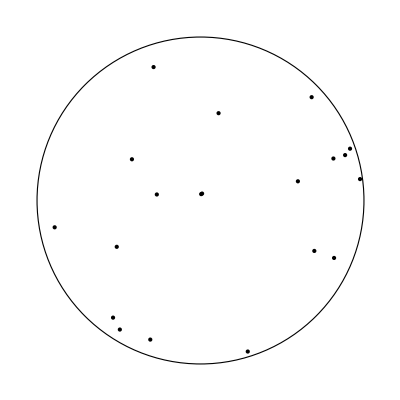

```mathematica
clusterPointsXY=RandomPoint[Disk[{1, 1}, 1], 20];
Graphics[{FaceForm@None,EdgeForm@Black, Disk[{1, 1}, 1], Point@clusterPointsXY}]
```

### Single hill

```mathematica
hillFunction[center_,x_,y_]:=Exp[-1/12 Norm[{x,y}-center]^2];
terrain[x_,y_]:=Total[(hillFunction[#1,x,y]&)/@{{0,0}}];
Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-7.5, 7.5}, {0, 1}},Mesh->None,ColorFunction->"Aquamarine",(*PerformanceGoal->"Quality",*)Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
clusterCenter={0,-4}; 
clusterPointsXY=RandomPoint[Disk[clusterCenter, 2], 30];
clusterPoints=Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]]+0.05},{p,clusterPointsXY}];
ptslist = NestList[
With[{survivors = TakeLargestBy[#, Last, 15]}, 
Join[survivors, 
Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]](*+0.075*)}, {p, 
survivors[[All, ;;2]]+ RandomVariate[NormalDistribution[0, .5], {15, 2}]}]]]&, clusterPoints, 7];
lps = Transpose[ptslist];
lines = (Line/@Partition[#, 2, 1])&/@ lps;
slines  = Map[Style[#, Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[1, 2, 3]]]]&, lines, {2}];
slist = Map[Style[Point[#], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]]]&, ptslist, {2}];
Graphics3D[{slist, PointSize[Large], slines}]
```

-Graphics3D-

```mathematica
gs = Show[Plot3D[terrain[x,y],{x,-15,15},{y,-15,15},PlotRange->{{-7.5, 7.5}, {-7.5, 7.5}, {0, 1}},Mesh->None,ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False], Graphics3D[{PointSize[0.015],#}]]&/@ lines;
```

```mathematica
GraphicsGrid[Partition[Show[Plot3D[terrain[x,y],{x,-15,15},{y,-15,15},PlotRange->{{-7.5, 7.5}, {-7.5, 7.5}, {0, 1}},Mesh->None,ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False], Graphics3D[{ PointSize[.025],#}]]&/@slist, 4], ImageSize->{530, Automatic}]
```

-Graphics-

So here we’re just “shaking” the dots and selecting the ones that are highest on the hill. We imagine each dot as an organism. And from this we get the notion of adaptation to one’s environment, as well as the notion of equilibrium, when the dots  reach the top of the hill. And population geneticists use these fitness hills to model anything

eh So this gives

### Intro v6

There are essentially two models that we can use to explain what we see in biology. The first and more well-known idea is born out of Darwin’s natural selection, and simply states that given some variation between organisms, the organisms that aren’t as good at surviving will not be observed. To be more precise, we can imagine a fitness landscape…

So from this we get the notion of adapting to one’s environment. And we can imagine these hills as changes in one environment, or another organism entering the ecosystem etc.

From this we also can get an intuition for the different discrete species of organisms, as in:

This model was popularized by Seward Wright in 1950s  based on the mathematical ideas of population geneticists:

### V7

There are essentially two types of explanations for what we see in biology. The first and more well-known is Darwin’s idea of natural selection, where variation between organisms leads to adaptation over time. 

To make Darwin’s idea more concrete, we can imagine a

### Outtakes

```mathematica
clusterPoints[[;;15]]
```

{{-4.86071,0.365527,0.188068},{-5.95452,1.61948,0.0918672},{-5.87277,-0.174239,0.106323},{-4.36856,0.192831,0.253221},{-6.1304,-0.291519,0.0933305},{-5.42094,-1.24413,0.125936},{-6.56903,0.209677,0.0773326},{-6.90243,-1.75962,0.0645769},{-4.48225,-0.120249,0.23723},{-7.45233,0.700932,0.0593812},{-7.17515,-1.47482,0.0614303},{-7.93679,0.0648259,0.0552489},{-6.45978,-0.507708,0.0802312},{-6.13779,-1.08231,0.0892822},{-5.66327,-1.68766,0.104472}}

```mathematica
Graphics3D[MapThread[Arrow[{#1 ,Append[#1[[;;2]] + #2,#1[[3]]]}]&, {clusterPoints[[;;15]],RandomVariate[NormalDistribution[0, .5], {15, 2}]}]]
```

-Graphics3D-

Starting with a random arrangement of points, we then select the points with the highest elevation:

```mathematica
sur = Map[Style[Point[#], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]]]&, TakeLargestBy[clusterPoints, Last, 10]];
```

```mathematica
GraphicsRow[Show[Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-7.5, 7.5}, {0, 1}},Mesh->None,ColorFunction->"Aquamarine",(*PerformanceGoal->"Quality",*)Axes->False,Boxed->False],
Graphics3D[{PointSize[.015], #}]]&/@ {slist, sur}, ImageSize->{500, Automatic}]
```

-Graphics-

```mathematica
fills = Line[{MapAt[0&, #, 3], #}]&/@ clusterPoints;
```

```mathematica
Show[Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-7.5, 7.5}, {0, 1}},Mesh->None,ColorFunction->"Aquamarine",(*PerformanceGoal->"Quality",*)Axes->False,Boxed->False(*, PlotStyle->Opacity[.4]*)],
Graphics3D[{(*fills,*) PointSize[.0125], ss}]]
```

-Graphics3D-

With filling:

```mathematica
Show[Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-7.5, 7.5}, {0, 1}},Mesh->None,ColorFunction->"Aquamarine",PerformanceGoal->"Quality",Axes->False,Boxed->False, PlotStyle->Opacity[.6]],
Graphics3D[{fills, PointSize[.0125], ss}]]
```

-Graphics3D-

```mathematica
Graphics3D[{fills, PointSize[.0125], ss}]
```

-Graphics3D-

We then add more points based on the locations

And the point is that if we “shake” these points with some random variation like:

and then select the ones that have the highest elevation

In the early 20th Century, the population geneticist Sewall Wright established the concept of the “fitness landscape”. The idea was to imagine a topology:

```mathematica
ptslist = NestList[
With[{survivors = TakeLargestBy[#, Last, 15]}, 
Join[survivors, 
Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]](*+0.075*)}, {p, 
survivors[[All, ;;2]]+ RandomVariate[NormalDistribution[0, .5], {15, 2}]}]]]&, clusterPoints, 7];
lps = Transpose[ptslist];
lines = (Line/@Partition[#, 2, 1])&/@ lps;
slines  = Map[Style[#, Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[1, 2, 3]]]]&, lines, {2}];
slist = Map[Style[Point[#], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]]]&, ptslist, {2}];
Graphics3D[{slist, PointSize[Large], slines}]
```

```mathematica
fills = Line[{MapAt[0&, #, 3], #}]&/@ clusterPoints;
Show[Plot3D[terrain[x,y],{x,-13,15},{y,-12,15},PlotRange->All,Mesh->All,MeshStyle->Gray, ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False, ViewPoint->{-6, 2, 4.}], Graphics3D[{fills, PointSize[.0125], styled}]]
```

-Graphics3D-

And this discrete nature of the variation between organisms suggests that the real fitness landscape looks very much like the one above: with many different peaks and different species occupying those peaks.

And therefore the specific nature of the landscape is different for different environments. But is it possible to do say more than that. Are there any constraints
 could branch and end up having very different characteristics and filling two 

 it’s  that diversity can be grouped into   what this does is it gives us a model for how speciation can occur and be

### Leaf code

```mathematica
GraphicsColumn[GraphicsRow[Flatten@{Graphics[{Line[#[[1]]],With[{head=#[[1,1,2]]},{Disk[head,.1],Arrowheads[.125,1.5],Arrow[{{head[[2]]-.4,head[[2]]},{head[[2]]+.4,head[[2]]}}]}],Translate[{Line[Flatten[#[[1;;2]],1]],Disk[#,.1]&/@#[[2,All,2]]},{2.5,0}]},Sequence[ImageSize->{Automatic,40},Frame->True,FrameTicks->False,FrameStyle->AbsoluteThickness[1],PlotRange->{{-0.75,3.4},{-0.25,2.25}}]]&@#[[4]],Graphics[{AbsoluteThickness[.3],Line/@#},Sequence[Frame->True,FrameTicks->False,PlotRange->All,PlotRangePadding->Scaled[0.05],FrameStyle->AbsoluteThickness[1]]]&/@#}&@With[{grow=#},Table[NestWhileList[Flatten[With[{head=#[[2]],dir=#[[2]]-#[[1]]},{head,head+#}&/@ReIm@grow[dir[[1]]+dir[[2]] I]]&/@#,1]&,{{{0,0},{0,1}}},(Length[#]<500&)],{θ,120 °,15 °,-15 °}]],ImageSize->{750,Automatic}]&/@Table[Function[Evaluate@Table[With[{t=θ ((2 i-2)/(Length[lengths]-1)-1)},# lengths[[i]] (Cos[t]+Sin[t] I)],{i,Length[lengths]}]],{lengths,{{.4,.7,.4},{.5,.4,.5},{.5,.5,.5},{.5,.6,.5},{.55,.8,.55},{.7,.8,.7},{.65,.6,.65},{.5,.6,.6,.5},{.65,.65}}}],ImageSize->Large]
```

```mathematica
GraphicsColumn[GraphicsRow[Flatten@{Graphics[{Line[#[[1]]],With[{head=#[[1,1,2]]},{Disk[head,.1],Arrowheads[.125,1.5],Arrow[{{head[[2]]-.4,head[[2]]},{head[[2]]+.4,head[[2]]}}]}],Translate[{Line[Flatten[#[[1;;2]],1]],Disk[#,.1]&/@#[[2,All,2]]},{2.5,0}]},Sequence[ImageSize->{Automatic,40},Frame->True,FrameTicks->False,FrameStyle->AbsoluteThickness[1],PlotRange->{{-0.75,3.4},{-0.25,2.25}}]]&@#[[4]],Graphics[{AbsoluteThickness[.3],Line/@#},Sequence[Frame->True,FrameTicks->False,PlotRange->All,PlotRangePadding->Scaled[0.05],FrameStyle->AbsoluteThickness[1]]]&/@#}&@With[{grow=#},Table[NestWhileList[Flatten[With[{head=#[[2]],dir=#[[2]]-#[[1]]},{head,head+#}&/@ReIm@grow[dir[[1]]+dir[[2]] I]]&/@#,1]&,{{{0,0},{0,1}}},(Length[#]<500&)],{θ,120 °,15 °,-15 °}]],ImageSize->{750,Automatic}]&/@Table[Function[Evaluate@Table[With[{t=θ ((2 i-2)/(Length[lengths]-1)-1)},# lengths[[i]] (Cos[t]+Sin[t] I)],{i,Length[lengths]}]],{lengths,{{.4,.7,.4},{.5,.4,.5},{.5,.5,.5},{.5,.6,.5},{.55,.8,.55},{.7,.8,.7},{.65,.6,.65},{.5,.6,.6,.5},{.65,.65}}}],ImageSize->Large]
```

### Computational biology: where we’ve been and where we’re going v2

Ever since I could remember I’ve always been interested in biological life forms, and in particular human life. I still remember in like 4th grade writing this essay about the wonders of the human body. How did our body work? How did our brain work? Why do we act the way we do?

And I think since then, and in particular in the last few months, I’ve made significant progress on answering some of my most burning questions in biology.

So after finishing another post with SW, and being asked to summarize the Wolfram view of biology, I figured I’d do this as my version of a vacation. And it didn’t disappoint, because of my rekindled excitement around biology, the writing and research of this piece was relatively easy, and quite enjoyable. So I hope you enjoy reading it as much as I did writing it.

In trying to tell the story of biology, I will skip the stuff that everyone already knows, like Darwin’s selection, DNA, the cell etc. and instead focus on the less mainstream but, in my view, equally important contributions. We will then use this alternative history as a jumping off point for the future of biology.

In doing this, what I’ve found, and what I think the reader will find, is that, like most things in life, the field of biology is full of surprises, and these surprises have tremendous implications for our current lives, and for the lives of the generations to come.

So okay that’s an ambitious goal, where do we start. Well everyone has heard of Darwin’s idea of variation and selection, but can we be more precise about this. Well that’s really what the field of population genetics is. And it’s mainly formulated in the language of mathematics, but with modern computational tools, we can do much better. The core idea of population genetics, and really natural selection, is to imagine a three-dimensional “fitness landscape”:

```mathematica
hillFunction[center_,x_,y_]:=Exp[-1/12 Norm[{x,y}-center]^2];
terrain[x_,y_]:=Total[(hillFunction[#1,x,y]&)/@{{0,0}}];
Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-7.5, 7.5}, {0, 1}},(*Mesh->None,*)ColorFunction->"Aquamarine",(*PerformanceGoal->"Quality",*)Axes->False,Boxed->False, Mesh->All, MeshStyle->Gray, ViewPoint->{4, -2.4, 2.}]
```

-Graphics3D-

And we place a set of points into the landscape, corresponding to a population of organisms:

```mathematica
SeedRandom[6666];
clusterCenter={0, -6}; 
clusterPointsXY=RandomPoint[Disk[clusterCenter, 3], 40];
clusterPoints=Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]]+.05},{p,clusterPointsXY}];
```

```mathematica
slist = Map[Style[Ellipsoid[#,1.25*{.125,.125,.025}], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.](*White,LightBlue,  Blue*)},#[[3]]]]&, clusterPoints];
```

```mathematica
fills = Line[{MapAt[0&, #, 3], #}]&/@ clusterPoints;
```

```mathematica
Show[Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-8, 7.5}, {0, 1}},ColorFunction->(*"Aquamarine"*)"Aquamarine",PerformanceGoal->"Quality",Axes->False, Boxed->False,  Filling->Bottom, Mesh->All, MeshStyle->Gray],
Graphics3D[{fills,PointSize[.0125], slist}], ViewPoint->{4, -2.4, 2.}]
```

-Graphics3D-

To simulate natural selection, we discard the points with the lowest elevation, here shown in gray:

```mathematica
ss = 
Map[With[{sur =TakeLargestBy[clusterPoints, Last, 15]},
Style[Ellipsoid[#, 1.25*{.125,.125,.025}], If[MemberQ[sur, #],Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]], Lighter[Gray]]]
]&, clusterPoints];
```

```mathematica
Show[Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-8, 7.5}, {0, 1}},ColorFunction->(*"Aquamarine"*)"Aquamarine",PerformanceGoal->"Quality",Axes->False, Boxed->False,  Filling->Bottom, Mesh->All, MeshStyle->Gray, ViewPoint->{4, -2.4, 2.}],
Graphics3D[{fills,PointSize[.0125], ss}]]
```

-Graphics3D-

We remove the gray points, and add new points closer to the survivors, with some randomness

```mathematica
SeedRandom[3333];
new = With[{sur =TakeLargestBy[clusterPoints, Last, 15]},
Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]](*+0.075*)}, {p, 
sur[[All, ;;2]]+ RandomVariate[NormalDistribution[0, .5], {15, 2}]}]
];
```

```mathematica
ssr = Map[With[{sur =TakeLargestBy[clusterPoints, Last, 15]},
Style[Ellipsoid[#,1.25*{.125,.125,.025}], If[MemberQ[sur, #] || MemberQ[new, #],Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]], Lighter[Gray]]]
]&, Join[new,TakeLargestBy[clusterPoints, Last, 15]]];
```

```mathematica
fills = Line[{MapAt[0&, #, 3], #}]&/@ Join[new,TakeLargestBy[clusterPoints, Last, 15]];
```

```mathematica
Show[Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-8, 7.5}, {0, 1}},ColorFunction->(*"Aquamarine"*)"Aquamarine",PerformanceGoal->"Quality",Axes->False, Boxed->False,  Filling->Bottom, Mesh->All, MeshStyle->Gray, ViewPoint->{4, -2.4, 2.}],
Graphics3D[{fills, PointSize[.0125], ssr}]]
```

-Graphics3D-

We repeat this process several times, and can see our “population” adapt to it’s environment and climb the fitness hill:

```mathematica
SeedRandom[3333];
new = With[{sur =TakeLargestBy[clusterPoints, Last, 15]},
Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]](*+0.075*)}, {p, 
sur[[All, ;;2]]+ RandomVariate[NormalDistribution[0, .5], {15, 2}]}]
];
```

```mathematica
SeedRandom[4444];
surs = Reap[ptslist = NestList[
With[{survivors = TakeLargestBy[#, Last, 15]}, 
Sow[survivors];
Join[survivors, 
Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]](*+0.075*)}, {p, 
survivors[[All, ;;2]]+ RandomVariate[NormalDistribution[0, .5], {15, 2}]}]]]&, Join[new,TakeLargestBy[clusterPoints, Last, 15]], 8]][[2, 1]];
```

```mathematica
highlighted = MapThread[
Function[{all, survivors}, 
Style[Ellipsoid[#, {.2,.2,.04}], If[MemberQ[survivors, #], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]],Gray]]&/@ all], {Most[ptslist], surs}];
```

```mathematica
allstyled = Map[Style[Ellipsoid[#, {.2,.2,.04}],Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]}, #[[3]]]]&,ptslist, {2}];
```

```mathematica
rif = Riffle[allstyled, highlighted];
```

```mathematica
GraphicsGrid[Partition[Map[Module[{},
fills = Line[{MapAt[0&, #, 3], #}]&/@ #[[All, 1, 1]];
Show[Plot3D[terrain[x,y],{x,-10,10},{y,-10,10},PlotRange->{{-7.5, 7.5}, {-8, 7.5}, {0, 1}},ColorFunction->"Aquamarine",PerformanceGoal->"Quality",Axes->False, Boxed->False,  Filling->Bottom, Mesh->All, MeshStyle->Gray, ViewPoint->{4, -2.4, 2.}],
Graphics3D[{fills, PointSize[.0125], #}], ImageSize->{200, Automatic}]]&,allstyled], 3], ImageSize->{525, Automatic}]
```

-Graphics-

Or as a video:
"/Users/erichegonzales/Documents/Wolfram/Video/AnimationVideo-2025-03-23T01-29-22.mp4"

And in population genetics, this hill is meant to correspond to things like a change in the climate, a competing organism doing an evolution of it’s own, a new parasite, an invasive species entering the ecosystem, or even a change in the organism itself leading to a new fitness landscape.

So okay, this model gives us an intuition for how natural selection works, but what else can this model show us? Another key point is that if we imagine not just a single hill but a whole landscape:

```mathematica
SeedRandom[RandomGeneratorState[…]];hillCenters=RandomReal[{-10,10},{5,2}];
hillFunction[center_,x_,y_]:=Exp[-(Norm[{x,y}-center]^2)/12]; 
terrain[x_,y_]:=Total[hillFunction[#,x,y]&/@hillCenters];
clusterCenter={-9, 1.5}; 
clusterPointsXY=RandomPoint[Disk[clusterCenter, 3], 200];
clusterPoints=Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]]+0.1},{p,clusterPointsXY}];
styled = Style[Ellipsoid[#, {.3,.3,.04}], Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]},#[[3]]]]&/@ clusterPoints;
```

```mathematica
Plot3D[terrain[x,y],{x,-13,15},{y,-12,15},PlotRange->All,Mesh->All,MeshStyle->Gray, ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False, ViewPoint->{-6, 2, 4.}]
```

-Graphics3D-

And this idea is a very old one. [Give Seward Wright images and story]

And then we evolve a population starting from one of the valleys:

```mathematica
SeedRandom[4444];
surs = Reap[ptslist = NestList[
With[{survivors = TakeLargestBy[#, Last, 50]}, 
Sow[survivors];
Join[survivors, 
Table[{p[[1]],p[[2]],terrain[p[[1]],p[[2]]](*+0.075*)}, {p, 
survivors[[All, ;;2]]+ RandomVariate[NormalDistribution[0, .7], {50, 2}]}]]]&, clusterPoints, 11]][[2, 1]];
```

```mathematica
allstyled = Map[Style[Ellipsoid[#, {.3,.3,.04}],Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]}, #[[3]]]]&,ptslist, {2}];
```

```mathematica
GraphicsGrid[Partition[Map[Module[{},
fills = Line[{MapAt[0&, #, 3], #}]&/@ #[[All, 1, 1]];
Show[Plot3D[terrain[x,y],{x,-13,15},{y,-12,15},PlotRange->All,Mesh->All,MeshStyle->Gray, ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False, ViewPoint->{-6, 2, 4.}],
Graphics3D[{fills, PointSize[.0125], #}], ImageSize->{200, Automatic}]]&,allstyled], 3], ImageSize->{525, Automatic}]
```

-Graphics-

Or with all the points shown together:

```mathematica
allstyled = Map[Style[Ellipsoid[#,.5* {.3,.3,.04}],Blend[RGBColor/@{Hue[0.77, 0.78, 0.9],Hue[0.02, 1., 1.],Hue[0.08, 1., 1.]}, #[[3]]]]&,ptslist, {2}];
```

```mathematica
allfills = Line[{MapAt[0&, #, 3], #}]&/@ Catenate[allstyled][[All, 1, 1]];
Show[Plot3D[terrain[x,y],{x,-13,15},{y,-12,15},PlotRange->All,Mesh->All,MeshStyle->Gray, ColorFunction->"Aquamarine", PerformanceGoal->"Quality", Axes->False, Boxed->False, ViewPoint->{-6, 2, 4.}, ImageSize->{525, Automatic}],
Graphics3D[{allfills, PointSize[.0125], #}]]&[Catenate[allstyled]]
```

-Graphics3D-

A key characteristic of biological life is the diversity of form; There are many different approaches to the problem of survival. But it’s not just smooth variation across life forms, there are clearly discrete categories of organisms in the form of species. So we can think about each peak in our landscape as a different niche. And this example illustrates how a single population could start out with a similar form, and then have some change in the environment, where natural selection then pulls them apart into separate species.

Another important note here, you may have noticed that neither population found the global maximum. This is the glaring weakness of natural selection and it’s one we will revisit.

So, as I mentioned, population geneticists usually think of the hills as some particular feature of the environment that gives one organism in a population an advantage over another.

But the question is, first of all, are all the fitness landscapes different for different environments? Are there any universal characteristics that every successful organism must have?

And secondly, are there any other forms of constraints besides natural selection, say for instance, the laws of physics, that also influence the forms and behavior we observe in biology?

Well, it turns out yes, there are, and some would argue, including SW, that the physical limitations are often more impactful than the evolutionary ones.

In New Kind of Science, SW explored this question with respect to computational irreducibility.

So in new kind of science, SW establishes a boundary between simple systems and complex systems, which he determines based on just looking at the system visually. Here’s an example of a simple system:

```mathematica
ArrayPlot[CellularAutomaton[250,CenterArray[{1},33],15],Mesh->True,MeshStyle->GrayLevel[.15]]
```

-Graphics-

And here is his quintessential example of a complex system:

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},50],Mesh->False,MeshStyle->GrayLevel[.15]]
```

-Graphics-

And the claim is that the threshold from simple to complex is surprisingly low. So to generate the above it just takes 8 rules. But what you get is something with virtually unbounded complexity. And therefore, you’d imagine in the real world that this type of complex behavior is everywhere.

Relating this to biology, it is sometimes believed that all the intricate details of an organism are a result of selection. But because of how cheap complexity actually is, you’d imagine that many of these details are not essential to the functioning of the organism and are instead just a natural side effect of the organism running a simple program. 

Pigmentation patterns of mollusc shells for example, are not exposed during the organisms lifetime and therefore have no effect on selection. But as you can see they are very complex and look remarkably similar to the behavior above.

-Graphics-

But even in cases where selection is acting on the behavior, you can still observe this phenomenon. For example, there was likely some selection pressure for a Jaguar to be somewhere in between black and yellow. But the exact location of the black and yellow spots isn’t a result of meticulous selection, rather it’s just a side effect of the computational irreducibility of the process that produces the pigmentation pattern.

But how does SW know this? How powerful is natural selection really and would it be able to evolve to something as detailed as a the coat pattern of a jaguar?

He answers this by looking at different constraint satisfaction problems... [get relevant pictures]

And what these show is for anything besides the simplest constraints, adaptive search inevitably gets stuck before it can get to the detailed pattern. And the only way to prevent this is to add significant randomness to the search, but this slows down the process too much for it to happen on an evolutionary timescale.

So okay, SW makes a strong case that pigment patterns can mostly be explained not by natural selection, but by the fact, which he establishes in NKS, that simple programs can produce complex behavior. But big deal, who cares about pigmentation? What about other, more essential aspects of organisms?

To answer this, SW explores the growth of different organisms and what NKS has to say about that.

He looks at the growth of leaves, showing that simple substitution systems can match the different leaf shapes observed in biology. The claim is then that these shapes didn’t arise through natural selection but rather just from the fact that the program for generating such a shape is easy to find.

He strengthens his argument by showing that the variation between leaf shapes in different species of plants can be achieved by simply tweaking the underlying simple program.

I think it’s worth pausing on this point, and examining these leaf shapes because I actually think this is one area where there is more to say since NKS was published.

So you could ask, what other simple programs could be used to grow a leaf? Clearly, all the ones we observe in nature have some sort of fractal tree-like shape. But you can also imagine a simple program that just goes from the root to every single plant cell. Or the opposite, a leaf with just a single large stem. Both of these are quite simple, and yet we don’t observe them? Why is this?

Importantly, the stems of a leaf are not just structural, they carry energy to the cells in the leaf. And, we can actually show that the most efficient way to do this is via a fractal network: [show minimal energy network stuff]

The problem is simply how to transport a lot of something in one place, to many different places. And this is actually quite a general problem and quite a general solution, and therefore, we’d expect it to pop up all over the place. We can see it in metabolism, circulatory system.

But one subtle case of this is information, and I suspect we can observe this in information networks like the eye to brain, or in companies, etc.

But okay, coming back to Wolfram

, is not a result of meticulous selection, but just a small change to the underlying simple program. A